```mathematica
SetDirectory["/Users/questmac/Public/lambda/julia/julia-ml-alfa/data"];
data = Association/@ Import["complete.json"];
tdata = Map [KeyTake[#,{"pageview","seoduration","totalduration","revenue"}]&, data];
totRevenue = Map[{#["totalduration"], #["revenue"]}&, tdata];
pvRevenue= Map[{#["pageview"],#["revenue"]}&, tdata];
ftotRevenue= Fit[totRevenue,{1,x,x^2},x];
fpvRevenue = Fit[pvRevenue,{1,x,x^2},x];
Show[ListPlot[totRevenue],Plot[ftotRevenue,{x,0,6000000}],ImageSize-> Large];
flm = LinearModelFit[totRevenue,{1,x,x^2},x];
```

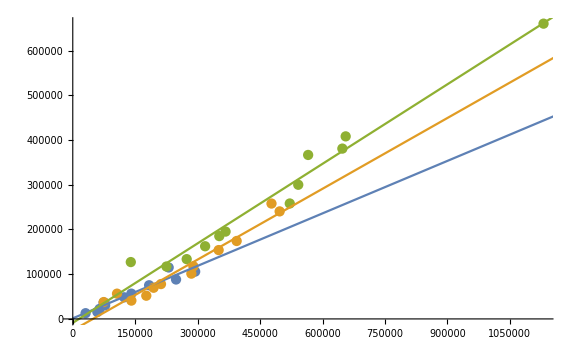

```mathematica
partTotRev = Partition[totRevenue,12];
fpsTotRev = Map[Fit[#,{1,x},x]&,partTotRev];
Show[ListPlot[partTotRev], Plot[fpsTotRev,{x,0,6000000}],ImageSize-> Large]
```

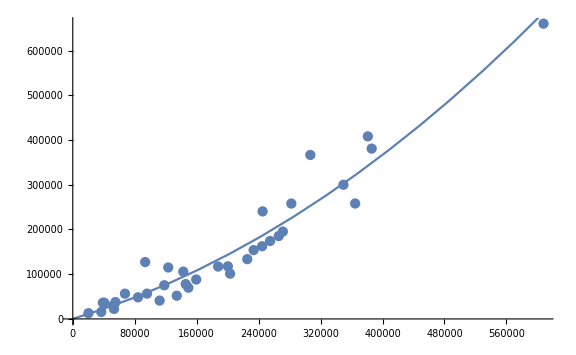

```mathematica
pvRevenue= Map[{#["pageview"],#["revenue"]}&, tdata];
fpvRevenue = Fit[pvRevenue,{1,x,x^2},x];
partPVRev = Partition[pvRevenue,12];
fpsPVRev = Map[Fit[#,{1,x},x]&,partPVRev];
Show[ListPlot[pvRevenue],Plot[fpvRevenue,{x,0,2000000}],ImageSize->Large]
```

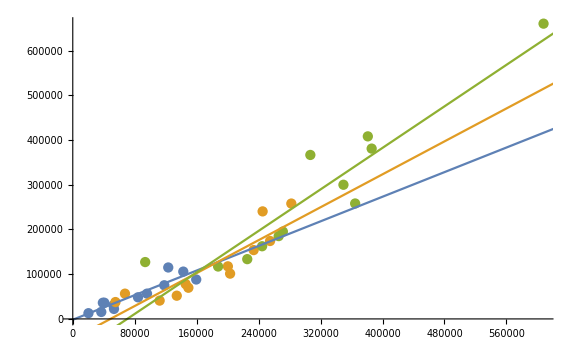

```mathematica
Show[ListPlot[partPVRev],Plot[fpsPVRev,{x,0,1000000}],ImageSize-> Large]
```

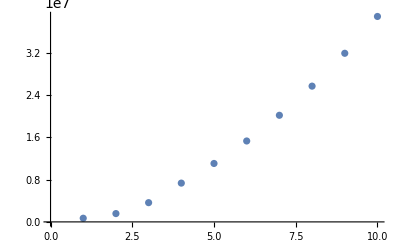

```mathematica
totDurOnly = Map[#["totalduration"]&,data];
ftotDur = TimeSeriesModelFit[ TimeSeries[totDurOnly]];
proTotDur = ftotDur /@ Range[1,36+84];
proTotDurRev = Map[ftotRevenue /. x-> #&, proTotDur];
ListPlot[Map[Fold[Plus,#]&,Partition[proTotDurRev,12]]]
```

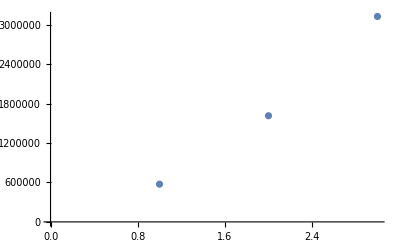

```mathematica
comp = Map[Values[#]&,tdata];
fcomp=Fit[comp, {1, a, b,c}, {a,b,c}];
ListPlot[Map[Fold[Plus,#]&, Partition[Map[fcomp /. {a-> #[[1]], b-> #[[2]],c-> #[[3]]}&,comp],12]]]
```

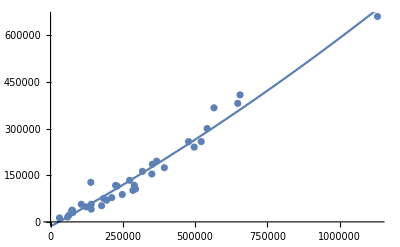

```mathematica
Show[ListPlot[totRevenue],Plot[flm["BestFit"],{x,0,1200000}]]
```

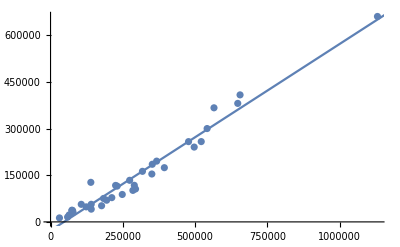

```mathematica
flmTDR = LinearModelFit[totRevenue,{1,x},x];
flmTDR["RSquared"];
Show[ListPlot[totRevenue], 
Plot[flmTDR["BestFit"], {x,0,1200000}]]
```

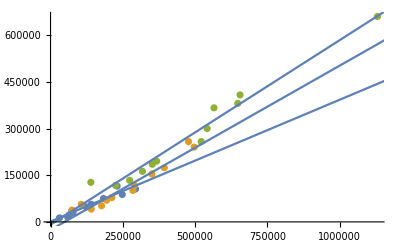

```mathematica
partTDR = Partition[totRevenue,12];
flmsTDR = Map[LinearModelFit[#,{1,x},x]&,partTDR];
#["RSquared"]& /@ flmsTDR;
Show[ListPlot[partTDR],
Plot[Map[#["BestFit"]&,flmsTDR],{x,0,1200000}]]
```

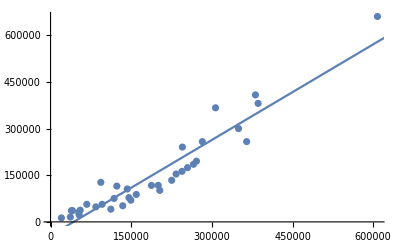

```mathematica
flmPVR = LinearModelFit[pvRevenue,{1,x},x];
flmPVR["RSquared"];
Show[ListPlot[pvRevenue],
Plot[flmPVR["BestFit"],{x,0,1200000}]]
```

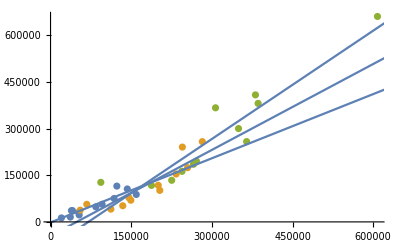

```mathematica
partPVR = Partition[pvRevenue,12];
flmsPVR = Map[LinearModelFit[#,{1,x},x]&,partPVR];
Map[Sqrt,#["RSquared"]& /@ flmsPVR];
Show[ListPlot[partPVR],
Plot[Map[#["BestFit"]&,flmsPVR],{x,0,1200000}]]
```

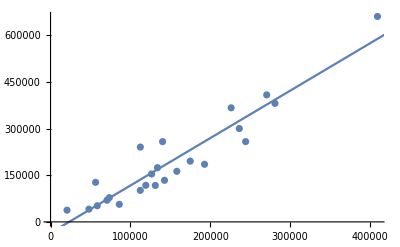

```mathematica
seoRevenue = Map[{#["seo"],#["revenue"]}&,data];
seoRevenue = Drop[seoRevenue,12];
flmSR = LinearModelFit[seoRevenue,{1,x},x];
Sqrt[flmSR["RSquared"]];
Show[ListPlot[seoRevenue],
Plot[flmSR["BestFit"],{x,0,1000000}]];
```

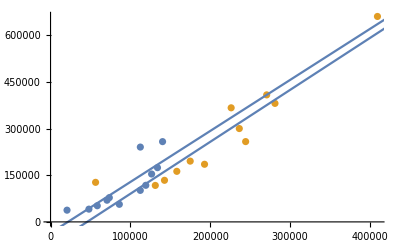

```mathematica
partSR = Partition[seoRevenue,12];
flmsSR = Map[LinearModelFit[#,{1,x},x]&,partSR];
Map[Sqrt,#["RSquared"]& /@ flmsSR];
Show[ListPlot[partSR],
Plot[Map[#["BestFit"]&,flmsSR],{x,0,1200000}]]
```